```mathematica
f[x_]=33Cos[x^2];
all[n_,a_,b_]:=Module[{x,xi,Δx,mid,trapz,left,right,simpsons},
Δx=(b-a)/n;
xi[i_]=a+i Δx;

left=Δx∑_(i=0)^(n-1) f[xi[i]];
right=Δx∑_(i=1)^n f[xi[i]];
mid=Δx∑_(i=1)^n f[(xi[i]+xi[i-1])/2];
trapz=Δx/2(f[a]+2∑_(i=1)^(n-1) f[xi[i]]+f[b]);
simpsons=Δx/3(f[a]+4*Sum[f[i],{i,a+Δx,b-Δx,2*Δx}]+2Sum[f[i],{i,a+2Δx,b-2Δx,2*Δx}]+f[b]);

{left,right,mid,trapz,simpsons}//N]
all[8,0,1]
```

29.8855

```mathematica
ClearAll[f]
```

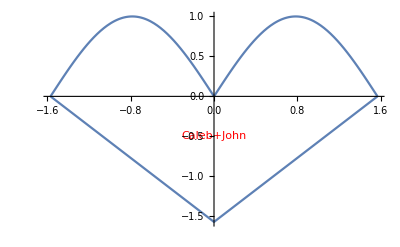

```mathematica
first[x_,y_]=Sin[2x];
second[x_,y_]=Abs[Sin[2x]];
third[x_,y_]=Abs[x]-π/2;
fplot=Plot[first[x,y],{x,0,π/2}];
splot=Plot[second[x,y],{x,-π/2,0}];
tplot=Plot[third[x,y],{x,-π/2,π/2}];
text=Graphics[Text[Style[John + Caleb,Large,Red],{0,-0.5}]];
Show[{fplot,splot,tplot,text},PlotRange->All]
```